```mathematica
(*This is for Fig 3*)
```

### (a) The phase diagram

```mathematica
(*export the data*)
(*note: the filepath should be modified accordingly*)
PRplot=Import["/users/linzhixing/desktop/data/chiralPR.txt", "Table"];
```

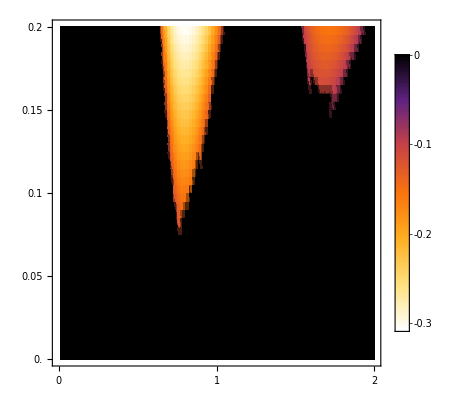

```mathematica
p1=ListDensityPlot[PRplot,PlotRange->{{0,2},Automatic,{Min[Chop[Flatten[PRplot[[All,{3}]]]]],Max[Chop[Flatten[PRplot[[All,{3}]]]]]}},ColorFunction->ColorData[{"SunsetColors","Reverse"}],
PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->20,FontColor->Black}],
FrameTicks->{{Range[0,0.2,0.05],None},{Range[0,4,1],None}},
FrameTicksStyle->Directive[Black,22],
FrameStyle->AbsoluteThickness[1.5],
Frame->True]
```

```mathematica
(*Analytical method*)
(*A0=-0.3;
boundary=Table[{invω,A,If[PossibleZeroQ[Im[ArcCos[MathieuC[4(1+2A0)invω^2,-4A invω^2,π]]]/π],0,1]},{A,0,0.2,0.001},{invω,0.01,2.05,0.005}];
boundplot=Flatten[boundary,1];*)
```

```mathematica
(*save the data*)
(*Export["/users/linzhixing/desktop/boundary.txt",boundplot,"Table"];*)
```

```mathematica
boundplot=Import["/users/linzhixing/desktop/data/boundary.txt", "Table"];
```

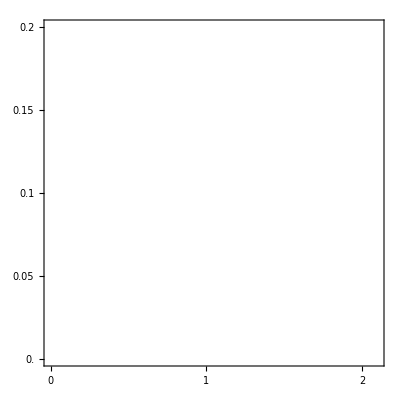

```mathematica
p2=ListContourPlot[boundplot,PlotRange->{{0,2.1},Automatic,{0,Max[Chop[Flatten[boundplot[[All,{3}]]]]]}},ColorFunction->Function[{z},ColorData["SunsetColors"][z-0.05]],
Contours->{0.0002},ContourShading->None,InterpolationOrder->10,ContourStyle->Directive[White,Thickness[0.006],Dashing[{0.02, 0.02}]],
PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->20,FontColor->Black}],
FrameTicks->{{Range[0,0.2,0.05],None},{Range[0,4,1],None}},
FrameTicksStyle->Directive[Black,22],
FrameStyle->AbsoluteThickness[1.5],
Frame->True]
```

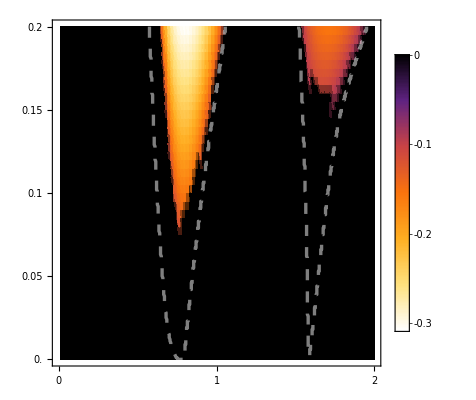

```mathematica
Show[p1,p2]
```

### (b) ImΛ curve

```mathematica
(*export the data*)
cv1=Import["/users/linzhixing/desktop/data/Lambda_01_5.txt", "Table"];
cv2=Import["/users/linzhixing/desktop/data/Lambda_01_10.txt", "Table"];
cv3=Import["/users/linzhixing/desktop/data/Lambda_01_15.txt", "Table"];
cv4=Import["/users/linzhixing/desktop/data/Lambda_01_18.txt", "Table"];
```

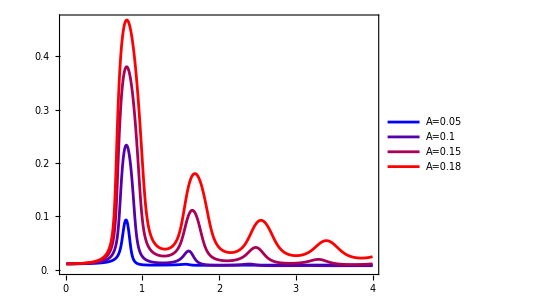

```mathematica
ListLinePlot[{Chop[cv1],Chop[cv2],Chop[cv3],Chop[cv4]},
PlotRange->Full,AspectRatio->0.75,
PlotStyle->{Blend[{Blue,Red},0],Blend[{Blue,Red},1/3],Blend[{Blue,Red},2/3],Blend[{Blue,Red},1]},
PlotLegends->Placed[{"A=0.05", "A=0.1","A=0.15","A=0.18"},{0.8, 0.7}],
LabelStyle->{FontSize->16},
FrameTicks->{{Range[0,0.64,0.1],None},{Range[0,4,1],None}},
FrameStyle->Directive[Black,22],
(*FrameLabel->{Style["1/ω",FontSize->20,FontColor->Black,FontFamily->"Helvetica"],
Style["4|ImΛ|-γ", FontSize->20,FontColor->Black,FontFamily->"Helvetica"]},*)
Frame->True]
```

### (c)(d) chiral-normal transition (new version)

```mathematica
pr1=Import["/users/linzhixing/desktop/data/normal_1_10.txt","Table"];
pr2=Import["/users/linzhixing/desktop/data/normal_1_12.txt","Table"];
pr3=Import["/users/linzhixing/desktop/data/normal_1_14.txt","Table"];
```

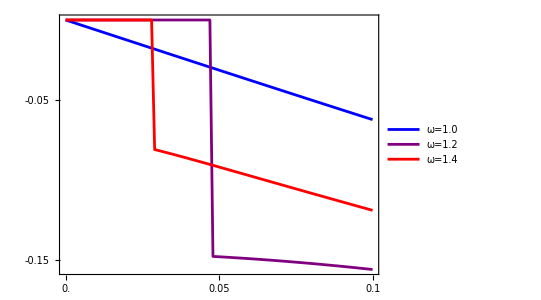

```mathematica
ListLinePlot[{Chop[pr1],Chop[pr2],Chop[pr3]},
PlotRange->Full,AspectRatio->0.75,
PlotStyle->{Blend[{Blue,Red},0],Blend[{Blue,Red},1/2],Blend[{Blue,Red},1]},
PlotLegends->Placed[{"ω=1.0","ω=1.2","ω=1.4"},{0.2,0.25}],
LabelStyle->{FontSize->16},
FrameTicks->{{Range[-0.35,0,0.05],None},{Range[0,0.1,0.05],None}},
FrameStyle->Directive[Black,22],
(*FrameLabel->{Style["γ",FontSize->20,FontColor->Black,FontFamily->"Helvetica"],
Style["ImΛn+ImΛp", FontSize->20,FontColor->Black,FontFamily->"Helvetica"]},*)
Frame->True]
```

```mathematica
pr4=Import["/users/linzhixing/desktop/data/normal_10_125.txt","Table"];
pr5=Import["/users/linzhixing/desktop/data/normal_15_125.txt","Table"];
pr6=Import["/users/linzhixing/desktop/data/normal_18_125.txt","Table"];
```

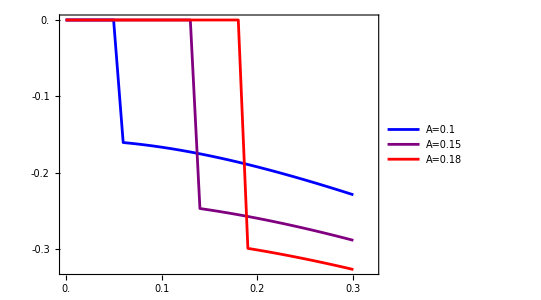

```mathematica
ListLinePlot[{Chop[pr4],Chop[pr5],Chop[pr6]},
PlotRange->{{0,0.32},Full},AspectRatio->0.75,
PlotStyle->{Blend[{Blue,Red},0],Blend[{Blue,Red},1/2],Blend[{Blue,Red},1]},
PlotLegends->Placed[{"A=0.1","A=0.15","A=0.18"},{0.2,0.25}],
LabelStyle->{FontSize->16},
FrameTicks->{{Range[-0.3,0,0.1],None},{Range[0,0.35,0.1],None}},
FrameStyle->Directive[Black,22],
Frame->True]
```

### (c)(d) chiral-normal transition (old version; but modified)

```mathematica
pr1=Import["/users/linzhixing/desktop/data/chiral_1_10.txt","Table"];
pr2=Import["/users/linzhixing/desktop/data/chiral_1_12.txt","Table"];
pr3=Import["/users/linzhixing/desktop/data/chiral_1_14.txt","Table"];
```

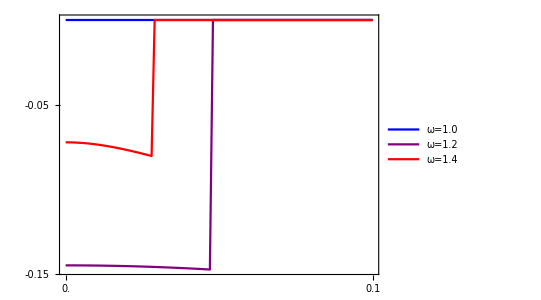

```mathematica
ListLinePlot[{Chop[pr1],Chop[pr2],Chop[pr3]},
PlotRange->Full,AspectRatio->0.75,
PlotStyle->{Blend[{Blue,Red},0],Blend[{Blue,Red},1/2],Blend[{Blue,Red},1]},
PlotLegends->Placed[{"ω=1.0","ω=1.2","ω=1.4"},{0.8,0.25}],
LabelStyle->{FontSize->16},
FrameTicks->{{Range[-0.35,0,0.05],None},{Range[0,0.3,0.05],None}},
FrameStyle->Directive[Black,22],
(*FrameLabel->{Style["γ",FontSize->20,FontColor->Black,FontFamily->"Helvetica"],
Style["ImΛn+ImΛp", FontSize->20,FontColor->Black,FontFamily->"Helvetica"]},*)
Frame->True]
```

```mathematica
pr4=Import["/users/linzhixing/desktop/data/chiral_10_125.txt","Table"];
pr5=Import["/users/linzhixing/desktop/data/chiral_15_125.txt","Table"];
pr6=Import["/users/linzhixing/desktop/data/chiral_18_125.txt","Table"];
```

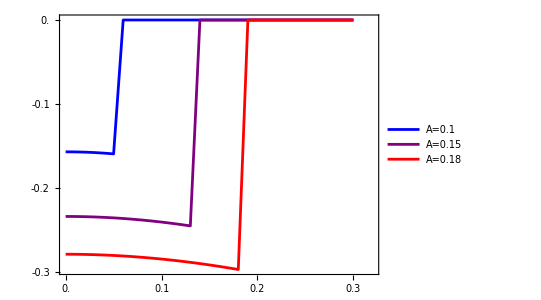

```mathematica
ListLinePlot[{Chop[pr4],Chop[pr5],Chop[pr6]},
PlotRange->{{0,0.32},Full},AspectRatio->0.75,
PlotStyle->{Blend[{Blue,Red},0],Blend[{Blue,Red},1/2],Blend[{Blue,Red},1]},
PlotLegends->Placed[{"A=0.1","A=0.15","A=0.18"},{0.8,0.25}],
LabelStyle->{FontSize->16},
FrameTicks->{{Range[-0.3,0,0.1],None},{Range[0,0.35,0.1],None}},
FrameStyle->Directive[Black,22],
Frame->True]
```